From Salvador e.a. 1997 J Chrom A V785 p195-204

```mathematica
data ={{"Compoud", "Class","k'", "OHn"}
,{"L-Rhamnose", "MS", 2.3, 4}
,{"o-Ribose", "MS",2.1, 4}
,{"D-Xylose", "MS",2.5,4}
,{"L-Arabinose", "MS",2.5,4}
,{"Fructose", "MS",3.3,5}
,{"Sorbose", "MS",3.4,5}
,{"D-Mannose", "MS",3.7,5}
,{"D-Galactose", "MS",4.3,5}
,{"D-Glucose", "MS",4.3,5}
,{"m-Erythritol", "PO",2.4,4}
,{"Xylitol", "PO",3.7,5}
,{"Mannitol", "PO",5.5,6}
,{"MGDG", "GL",2.1,4}
,{"GSS", "GL",2.7,3}
,{"GalCer1", "GL",6,5}
,{"DGDG", "GL",14,7}
}
```

{{Compoud,Class,k',OHn},{L-Rhamnose,MS,2.3,4},{o-Ribose,MS,2.1,4},{D-Xylose,MS,2.5,4},{L-Arabinose,MS,2.5,4},{Fructose,MS,3.3,5},{Sorbose,MS,3.4,5},{D-Mannose,MS,3.7,5},{D-Galactose,MS,4.3,5},{D-Glucose,MS,4.3,5},{m-Erythritol,PO,2.4,4},{Xylitol,PO,3.7,5},{Mannitol,PO,5.5,6},{MGDG,GL,2.1,4},{GSS,GL,2.7,3},{GalCer1,GL,6,5},{DGDG,GL,14,7}}

```mathematica
data //TableForm
```

Compoud | Class | k' | OHn
L-Rhamnose | MS | 2.3 | 4
o-Ribose | MS | 2.1 | 4
D-Xylose | MS | 2.5 | 4
L-Arabinose | MS | 2.5 | 4
Fructose | MS | 3.3 | 5
Sorbose | MS | 3.4 | 5
D-Mannose | MS | 3.7 | 5
D-Galactose | MS | 4.3 | 5
D-Glucose | MS | 4.3 | 5
m-Erythritol | PO | 2.4 | 4
Xylitol | PO | 3.7 | 5
Mannitol | PO | 5.5 | 6
MGDG | GL | 2.1 | 4
GSS | GL | 2.7 | 3
GalCer1 | GL | 6 | 5
DGDG | GL | 14 | 7

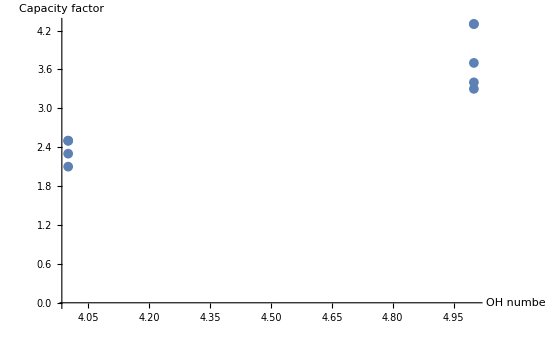

```mathematica
ListPlot[Select[data, #[[2]]== "MS"&][[All,{4,3}]]
, PlotRange->All
, AxesLabel->{"OH number","Capacity factor"}
, PlotLabel->""
]
```